```mathematica
N[Log[2,.95]]
```

-0.0740006

```mathematica
1250/3
```

1250/3

```mathematica
N[1250/3]
```

416.667

```mathematica
N[625/2]
1200-3*290
```

312.5

330

```mathematica
fun[x_,k_]:=N[(Binomial[500,k-x]*Binomial[500,k+3x])/Binomial[1000,600-2x]];
fun2[x_,k_]:=N[(Binomial[500,k+x]*Binomial[500,k-3x])/Binomial[1000,600-2x]];

fun3[x_]:=N[(Binomial[500,x]*Binomial[500,1200-3x])/Binomial[1000,1200-2x]];
fun4[x_,y_]:=N[(Binomial[500,x]*Binomial[500,500-y])/Binomial[1000,(x+y)]];
```

```mathematica
1200/2
```

600

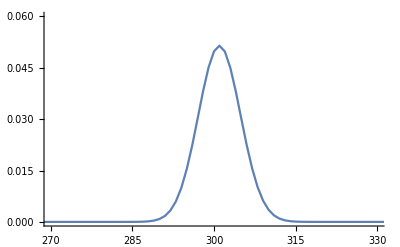

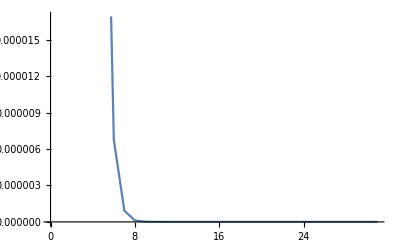

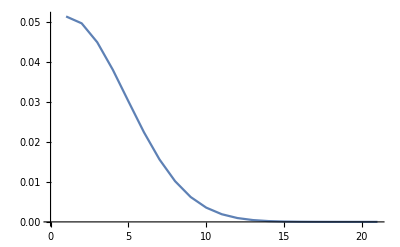

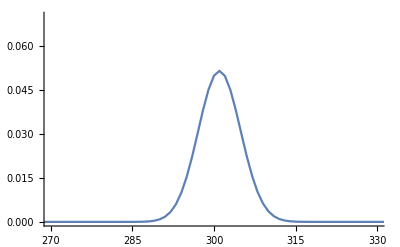

{{290,0.00174603},{291,0.00334423},{292,0.00596849},{293,0.00993138},{294,0.0154159},{295,0.0223341},{296,0.0302148},{297,0.0381872},{298,0.0451075},{299,0.049818},{300,0.0514625},{301,0.0497407},{302,0.0449974},{303,0.0381106},{304,0.0302276},{305,0.0224577},{306,0.0156326},{307,0.0101973},{308,0.00623449},{309,0.00357314},{310,0.00191994}}

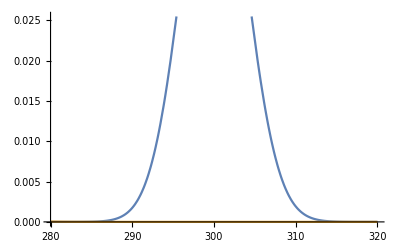

```mathematica
t1=Table[fun[x,300],{x,0,30}];
t2=Table[fun2[x,300],{x,0,20}];
t3=Table[If[x<278,0,fun3[x,300]],{x,0,400}];
ListLinePlot[t3,PlotRange->{{270,330},{0,.06}}]
ListLinePlot[t1]
ListLinePlot[t2]
ListLinePlot[t3,PlotRange->{{270,330},{0,.07}}]
t3=Table[{x,fun3[x,300]},{x,290,310}]
```

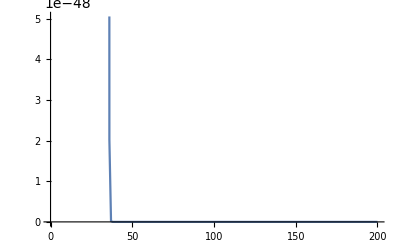

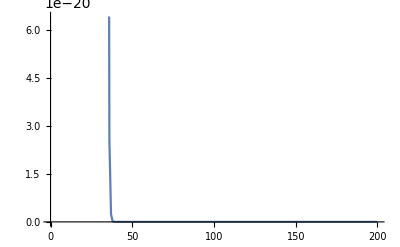

```mathematica
ListLinePlot[t1]
ListLinePlot[t2]
```

```mathematica
t
```

{10790473719844929400973922916399559259778807434007682803128579298612581756577166388257579203118738441476369834236846747359221658315544793544095804784488826432925792562525132353657200/1094712661867061868191957336308056499425839066747404021157120046560576430206750611061580977655872290474163908540585794956960716966032308221892554910246203260803358609187895840106848927,17397057354533190978885797528632922187703612678831355849011282427982949170706287019816840021490217972374005048264616093466068822140215569314023694513656233864256514118456908029368650/9852413956803556813727616026772508494832551600726636190414080419045187871860755499554228798902850614267475176865272154612646452694290773997032994192215829347230227482691062560961640343,323730814202526386872308839035930230014345522388959282407823505436292506245573899058275561006607877590684354230662440139640964209039149791816933107274663007395865496511543779102400/1094712661867061868191957336308056499425839066747404021157120046560576430206750611061580977655872290474163908540585794956960716966032308221892554910246203260803358609187895840106848927,811986521352607655970503461144454999553576782670392606545750231733876667636890386031571925938135937391967110020535571956171401353214966024501756940197043250092593281079595872030200/17544989418572099671292721633261554166473582880573259041788437502984373597637921955662635668917088331112951290934253416472370409752896183123845542210162122531253828520227627923874632803,2525309717887912656282048307223787569362334757415034750507683244367894461884804218058948484157497029830329796870472292451993708580086931451900992589412959180894275514653332571680/373297647203661695133887694324713918435608146395175724293371010701795182928466424588566716359938049598147899807111774818561072547933961343060543451280045160239443160004843147316481549,2515288390170900488170771547812875475219266221656143922448027152820135612911063274470433353803700227443801628083313074132707242906666549460858049585900695382973276282400111200/2724800344552275146962683900180393565223417126972085578783730005122592576120192880208516177809766785387940874504465509624533376262291688635478419352409088760871847883247030272383077,5451457240581093192914050992483863142411317496582099763305943397945036332820710985250776033097963556380105708095003112676862597325569049289971691390153979203059532804709404728300/46384276265313379826745768032770839660798229752445812807635435877201893423294043399789570894855659987658917506689516370338431664112991415641749132636059917976321466516514196326777119771,21816193858891645836180205397806751048265239513432333369212023794653671009658497875051258511386425003674794383734418809542750231516031786357262424903327781532270579858131540775/1563514930291462241350980944924859763847131339970083577785464130692198654717776743813131603197381797336817444045714034955228033621786227493542105594473929819426566287073512235734060217,199601445692877095952680084443694035378427139428058667281169470103468119217592845071356336515927842972002363686289368081967655821023643993533566338367620890706797459103600/129290906333536942144296778708745535751850768210541931512897058686198516060347039098084148118529876567999457871968414368248410950284150127639304192051098141025929569757174583290669,966688183435927036308763604848899869225091518194789896612015699638731930572706894174594226885059970212269679918741041725440659007056517908523499247576511005020958556201980/6076672597676236280781948599311040180336986105895470781106161758251330254836310837609954961570904198695974519982515475307675314663355055999047297026401612628218689778587205414661443,278128692062999021439235811832541248555819739206561225995062665995657484425310905536065662139052839243181943161015192248768083596120132876630732697986542052257260983404400/18230017793028708842345845797933120541010958317686412343318485274753990764508932512829864884712712596087923559947546425923025943990065167997141891079204837884656069335761616243984329,101518455165319072457631515006573891230595717708791470948890810522668690010784457657687080037162277010537758837689313908498904713455896048652928686005482233626417621741025/74600852954450815617259241314946174128817893257482694482941602861936543766820241559594553464391738779735687192125775090479333118313954623647878518813483627371961361749889734558716013,193550407214674766792843656297325984290526575963856992319740568325072661902718600300034476465693213729248597078780815758113025481381602349992184386495841384008664915559300/1715819617952368759196962550243762004962811544922101973107656865824540506636865555870674729681009991933920805418892827081024661721220956343901205932710123429555111320247463894850468299,20080974338870940799577912265575365574996785866848559936692941515295948727966925510256676081657331153983139388915639457452315551857890856093859263672670297568589904313200/2312626441587975284135036480763331397993354690981963528971189688720032856771427488347431157396143902171806302955899027804859326667732593333084234083217992448530802214246581771320196403,18835605654504248240791488849325739137666594324890867665147655319092558025777676519186527731226776232897287947897473877767794782251274051758260559587379311696317597023358160/30371723057374879406545434101864831249846727156666127025978634181960191507979157204466813390083557867222332176719821932161217537127332148243395246214901894826555025479700358402748139360599,663822847521648331793667108714065202621329074954353052701229720702865204712475039620246374511239488033251092174679472786049501036281767539703883259114961813074709248411727900/16166574263540093067335684132737792917861962735875734259860433633436294195908518484867964120960283495710829137033992958148137115488326057360137579283616005372031757272275342387217646696427229,366362276810212239267211075303286508668682984888259300409349693426054691287319954151760474907644252867362823190497477964356100976683915879883388073075951769818034035758248800/145499168371860837606021157194640136260757664622881608338743902700926647763176666363811677088642551461397462233305936623333234039394934516241238213552544048348285815450478081484958820267845061,238933471746481655312015974938128353349825463969428933188964983890180980602051737617280189163329374262110655818479237329798936389627361401801929292288890536906649050879350/1672404234159319972483001806834944094951237524400938026882113824148582158197432946710479046995891396108016807279378581877393494705688902485531473718994759176417078338511242315919066899630403,9099889723336472123674014496329825311198986518870720776101066206192211701035698465787535612466893048592616318131556741026396135305935715625213873285582714229846036002859600/1214480564652478925524721326595341213995966067176200024825827208501637771026069168997419907359755509924411567570258298581602258539390635316558341357067686928300442671127287227880531668692472509,3965918784393473474203271301637067919047713959772563405870309111803973213497767144200545824966179746353734143253198185554467073098157697096421119324130777695102176138344430/10930325081872310329722491939358070925963694604585800223432444876514739939234622520976779166237799589319704108132324687234420326854515717849025072213609182354703984040145585050924785018232252581,846244908807790842274448530680540826111993003360396103317768953187858567104351273986554499378888295596239020267277908469609380136406573914155766158643405626521502464984200/52222664280056593797563017043599672201826540888576601067510569965570424154120974266889056016469486926749697405521106839008897117193797318612008678353910537916919034858473350798862861753776317887,19391781348416565701594477691682119725354024838527693111418116635290745138622235225878715684045645881030433573596090602133014715720414835154658603785907316278987435149684200/29088024003991522745242600493285017416417383274937166794603387470822726253845382666657204201173504218199581454875256509327955694276945106466888833843128169619723902416169656394966613996853409063059,8246788341705543141721211118754711572533957158796518640662596236227302206200742999331769508357810344163489583695170794615398258844794829170964320507491554746525158111700/326831730381927221856658432508820420409184081740867042635993117649693553413993063670305665181724766496624510728935466396943322407606124791762795885877844602468807892316512993201872067380375382731,7649763120090207989192735134078702534310916297674800824876604725830081153461466981807532976598860301566752989308130012311942682112844982468737114279187010604738132467975/8718046389490012173711330746223651679286840505971499951243816417306941994554652186740479022405542027247170088513697208309162576779633142701207601886090413000737736104349776818663889797332338697499,1220352422570374471838134262407709257727494376018786379967976875672789431034166598285986224591141538608269211444302936750582174353600302368933425284046420113443394390656/43590231947450060868556653731118258396434202529857499756219082086534709972773260933702395112027710136235850442568486041545812883898165713506038009430452065003688680521748884093319448986661693487495,60063977583290623733692853262496928025233613123834360537310436068388710043439808326088486385737363655233211416384322387589246016766789168990774474769583277217323007200/73400326053448167010924429831108809299802108776082628621762454352164898728347232927073065317672466745532625583937902302215852662564008072419844648137728961070727391072106185473266943132378722582169,292799075368501890750241072989661163372504667739805314371294177741006388628985313778526940462041031711609285906765946614860927899616331936856787677736877837571991766400/13383326117078715784991887705872172895663917833505732618701354176878066534801978803702988909588946436602115398138010853104023802140837471871218340843779247235229294305480694484625672631137053750815481,49607195466627444716356367583299327802084168713568615203443479665692185989501820854075178254488827287749836938717986911092859292765441687814507015657985938092617183604175/92875822143820594642582036716184255838275701791918615796247830869474822396014132238097508702910758621206480157945082650257557178923365108962298212675546716063412892715267526158473959502547440679409166313,514649527243880538018639678633409114598775441538601276553999682106790689442982812516701286962374504353726347282827555741685394103838628261389474368313803309638362863397723900/43296373577437338973630557851403510474476335520681896316248136521393857127038109335525142244060981119446638307425889187920692544428437119551173995183924690285452393066658085176922990005726328669421405428836387,16929866799757310808706472625064252749198681494556867461426257102736061030291273005050667028737668827028513768390082075616593908652050421233168913961985643510676185320197240/70340354670851652807009404797625523023098190740807525246517242817039269386569420872429735597708681037899793766718937089084368367975328773805360754938448220553843077024210282524670683462756588018489430441442899,2855793279558133428137329354334644225271080526777104486915875857549963389028613133093896099411170875823034712847477044221642196722929729381938209451161748588669013107800/645324354778455530339535823831426816725671474686307571068965530431552930152013035526878308235859459063300860245127863202608884109865401594544594082004112115172872266277158555272208105162904477233847985701311,1677811506010123389227828341787730410059498681111460870934569734485535582116304824097632852934554112940936746103586982225035274299085650791082755068719522865183299308802450/22756072722552677366363051755767603838197353211863263878604931499607850975950435671784309783321112104949178234823943840113597080366183656428426021113711005517340994725731442134563874412359500580697181519785329793,5029440525608403833949412610038165846333831143409082409226214117718692201746179820110176682387926652305802779641072918371346973207521112458454582635908605391614923919365200/4528458471787982795906247299397753163801273289160789511842381368421962344214136698685077646880901308884886468729964824182605818992870547629256778201628490097950857950420556984778211008059540615558739122437280628807,68333788595940896163308669282164743342797044719649993197216695479738593835202709828676530667956363095816413280088279773521864186442164225139574693879823446259494224980650/4528458471787982795906247299397753163801273289160789511842381368421962344214136698685077646880901308884886468729964824182605818992870547629256778201628490097950857950420556984778211008059540615558739122437280628807,7517681798766432381218362892553702033937450466426481511998033296540983100497098313638152918783311239162840677266618562325432011580742424401844866163803450354667089644640/40756126246091845163156225694579778474211459602447105606581432315797661097927230288165698821928111779963978218569683417643452370935834928663311003814656410881557721553785012863003899072535865540028652101935525659263,15600449618952650006997262496594045523616309815769305370689803405490170703713046266607077443829502287193445473451667714263858239650774316248307207081729198738739065934546100/7711290037142638291991749120026763372732162021720739581030310955598706999807386891492583156068789674735937808163289330824174501477828604901027534017421275991785716411731595882086561393285196796744814473381445756044628757,51593244163438526776896691557865144674169363802982576938050216820799387177624635848642755070118583787335856602796653884485665767058087299100537112705897157331554212400/2599019223843154126050471560507840705336084267516258706110654181192688574252573943880210029008692172138839840971786090604709976905233773138196000679953244351798354031591370368077708592276776810497072623316968572984371,3222877610408331301283378142638350542474382620651566507455921400139332313174787006950273822876069277698899056222762167507859574014593270211097348763797903179684658800/18551619977087341520429228035349069862226532530202260419479497086444363271389062289075981931199975159749649899350335198454309145495979001365743866922424882097319285673772885041106402710389406888720483897469396365784993,1456930595909398285848463198107865838788904996471762237197633933030162258328247263106528845383436675614276346581682550773596362759835761654009194634805000533790378700/1078055249779631068353831806943062615327164057032864688820864108467822443437386619687415394446398556505451877484469478754622631454933001968253782488936468148544220711931468764055405401948184422533423675375166033256172371,5230121109861706668146697941707878286767525698397686395654695686027544842888483301576857464852322780292826936765602781124067389222685343184292664651149046707214539645/561666785135187786612346371417335622585452473714122502875670200511735493030878428857143420506573647939340428169408598431158390988020094025460220676735899905391538990916295226072866214415004084139913734870461503326465805291,148665641771040934507377853699012722475157128205930305874223656462981625714393606409264723040759787236308991832542779082297396633838791804340217770562421165269033200/2626171725091553704971241142032407100196845350068734945878133640230547034982215356548265182368574083608267407386694257529470314619661520713638329110143531990073952579149164165151509597129613690708245300880806488526448224739,1622700666968303333069306191013672343222373650088178019363096842714306797690755743622408479830087405820649255867080325369529274195775216541566601402123002276798900/5366524829534914092767318855457527552576162237096980106794447003949378723659309641642107111796651388242981223790201308864569773353221368414826150790293304501455468313913509380961780481090949715795109962669474128727959415771,83551079735417612227934494514077878758729577806223751960643936424353398354023340442214864707104713659349039764708886655477092334184606097163326811068017928467823600/59144470146304288216388621105997411156941884015045817756981600430526102913449251560537662479110894949825896067391808624996423472125852701299799007859822508910540716287640786887579782682103356817777906898580274372710840721212191,132939592476057035543185736107606586497281154312594595110848959062789689148674258422632209762248275725982165075926245526031669231198754384277511157485977487896725/23143488318119069302065112606694639148368563310235319991862365385858040270480141914992998361391219762975350635066359896737730923875333665726008307423408807834559410721250742695139914962562183102608746177705324754539024630039553,140230185086061400247670910722962047788034020240087715751038996059594909226204412076217977104752267994478647730277609449590282157573741175467286198451159465522860/6935331999329681100852178744472826864794446138633850890894755493962126067720549193859568508963568855638280073641552515722406700187974988495893822791214839414422970079468139227643594517114467536415087604585695651443527714135186049,13190789262800651419928808341079299488878206438626019426257207121976337135023240707321043021089339128971158861550597616457143993858004904128534346595781591745319805600/215348066888475350795187188286733569110874752859752506621770636577366950257939721038457882542837078406053864249874003744843515552507886241795870140349032219607045916067231235582951158323787543839397517726613956051654236100073872604297117,342065715843751620540619215816330495956938004968702281848635826500202883777193059349769898000311152882339861931054245218249129819109551630909082342219734523152800/2155876086758930096948481306541270436037678282244463358838638185980314296241888197270434864166333376701317884592731961850491256921658482954574895732081523889280771128592971212732547747401655055121888386584566857024347191213197834748247,109746702745776677798168373387030875106949898652060642395925959117311554615553424969960528693125413120876819315014217841750198794697014998960563846457556375759400/314518366879386135254817328387632009168607953842997821128347993132461407885066578112897886294488413734314486941139673989966113370904176457706315344024782318513961387982507911368648354704263676375004383509504031474774206895880973002716479,102256271500882825139628085945630546256610157756884132782625243556546000940059985551424843686456284299740031334464389284803093244713577263263959520021474412126400/158202738540331226033173116178978900611809800783027904027559040545628088166188488790787636806127672108360186931393256016952955025564800758226276618044465506212522578155201479418430122416244629216627204905280527831811426068628129420366388937,2031600974410745983134993451632797219854777385253709708299551334437176329968272945343048851795306101958444618903730289446485396106426080177564470262052129698166/2032296718171947288272300800145344338628633594674281536354027674701530055673344432927810411278717018622780862887897981140857191482255517432599091939494287656730097734762972850990602341808681006090518709167834472916346781035453662553937457883,15554400051052751531852232768828002673871044249529028879079069500731622262909165551866448619652644090810738796122041121004365122430420409153468526353849200/12169441426179325079474855090690684662446907752540608002119926195817545243552960676214433600471359392950783610107173539765611925043446212171252047541881962016347890627323190724494624801249586862817477300406194448600878928356009955412799149,388732315668365585813552261088008025810564862699657641097131033211581659050453033323648840968685921234673587452025952567222547694594425779782247350/290951310711735555277351830145820545021838995229415190683023120381555418950107842842643743103134517793075381074134758547609725597506176186592336118431806030077670109142005468426131687978042253815915248389920473149652365306087856616759,29230350238982257850673328355161252982134740753921834047454664149461773577200910404978769522503397263033845576579235298610299835222126770696600/25926354419857623737585806646657276289074761951136007090566416667663354163870995896869244434932778813244340887794186405232549805718372135438921040256299547234643871111663853622130546453488913706368685500091923349969022651037531777731,11573534500667631464403127983269981328205927220540157529800299547733150098301316792482585822121358576401794946424208370039714098529031273400/15289901324531419127294193663413265503813321150669952899564809829647619122282895016102374923165484941144098472288879162060221680295450233720389331433202297087097667578673554700230835087955000390935378628259339411520192845483672586867,3578976547166203287457341860723606723937469191028020895976215763684288914986308941119528547527774269116433534654545747488450427903519940/9001716627867547999631617618473166789736853775017870109174043246138316693472378925655556683644905672618562230902228137977825337646109862550510811367680985645907533171727259774399162242352027080190507784417253523874691138238259106479,177788143006202501394983385916292575449442182333635713738601241945035235013617617656158273481741086562342413866768639328873750669475/1109800680148053862968281624195321932981255944865216862774882044044450003304813840149315207572659603473521370933151414271238740257739572095268456196015463983742024637610210109172499454536551283859103699448702489244824934851292218607,9043284032274759923157659727977115252002265762082880654746401992046750439093938485387298889335919346762865393805300674848234400/186955670132467855052004431316057816667093295371559829929818838960893011309413084182859551096469538936399657469025507063613694595389820388808664663844898950666219204185232527351639693058128710900995963706412247292138967519751735751,666031472341000979693333513936859368204923651859659698426935893634336945381743157480831310321503804418580334983419559800/62589779086865703063945239811201143845695780171262078985543635407061604054038528350471895244884345141077890013065117865287477266618620819822117396667190810400475126945173259910157245750963746535318367494614076763354190666137173,50463085224695977084589118000312810806310783679738078283310322627407895665165382416327737252319024415781268033266400/30629040829742790861079585439523964009595807317851655673776672646008870068997577703422416821964679537123222772351015125566212279409112316083163832411604013600232508930616701658162056431322684474730264944172846075683965645130957,1323083658584474129133113993622081595026884395393718576030569894807738559392764552357573223900876478414155965/7697672990636539547896352208978126164763962633287674208036359046496323214123543026746020814768705588621066291116113376618801779193041547143293247653079671676359012045895124819844698776406806854669581539123610473909013733383,143581408228283688689183541274609997471729582956455969150811648879097076788069279506986038223222138954900/12573358378179837150210740364376939282560714397174300865717738097060213157810240145414325745428346364523085247101367530715163750658883601955743865168466028016471246163256720195178193202921674920007320325900561445866738362973,290656732649932772189856121847329841716654667755252474115918015060051012669792089774066179146867800/649102631378308992458298259728828605409444146699246889817168123557601826502631900432479531790755930864480500328368878258717822691758809278786012159748724199703104486439639474703271924433814957629441011088556709442451120077,2012425528832264320383218274965412754065394442476398688908924776915791622218085442866554383400/216367543792769664152766086576276201803148048899748963272389374519200608834210633477493177263585310288160166776122959419572607563919603092928670719916241399901034828813213158234423974811271652543147003696185569814150373359,268787465999388519696486997641664576967916998553622271330692980729948983370385968941868050/3101268127696365186189647240926625559178455367563068473570914368108542059957019079844068874111389447463629057124429085013874041749514310998644280318799460065248165879656055268026743638961560353118440386311993167336155351479,415134496438704754144409762214408076872836155712008723904643988245943882707938271920/1530115276613896623053871323028070455473680247512213367867691209974157802738718298372971599514315020393208287163470682776221408122161125086287631688481397121039265207164896833563289394648331289534807071507429521124265683811,25524182122639182400527215145846456653560929528354722315820974466455177623450/170012808512655180339319035892007828385964471945801485318632356663795311415413144263663511057146113377023143018163409197357934235795680565143070187609044124559918356351655203729254377183147921059423007945269946791585075979,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

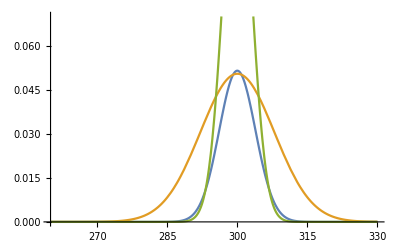

```mathematica
Plot[{fun3[x],fun4[x-50,500-(x-50)],PDF[NormalDistribution[300,Sqrt[300/32]],x]},{x,260,330}]
```

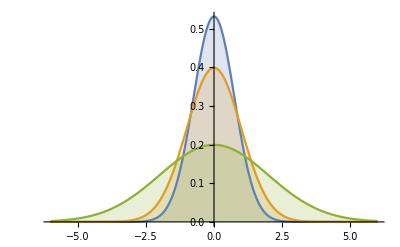

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}],{x,-6,6},Filling->Axis]
```

```mathematica
PDF[NormalDistribution[300,Sqrt[(300^2+300)/8]],300]
```

1/(5 √(903 π))

```mathematica
n=10000
f[n_,eps_]:=N[Binomial[n,(eps)*Log[2,n]]];
g[n_,eps_]:=N[Binomial[n,((eps))*Log[2,n]]*(n^(1-eps))];
deps=0.00001;
t1=Table[f[n,eps],{eps,0.8,1,deps}];
t2=Table[g[n,eps-deps],{eps,0.8,1,deps}];
ListLinePlot[{t1,t2}]
```

10000

-Graphics-

-Graphics-

```mathematica
J=1-IdentityMatrix[10];
MatrixForm[RowReduce[Transpose[AppendTo[J,{1,0,1,0,0,0,1,0,1,0}]]]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5/9
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/9
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5/9
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 4/9
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4/9
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 4/9
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -5/9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4/9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -5/9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4/9)

```mathematica
func[n_,k_,d_,i_]:=(((k+1-n)/(n-1))*(k*d-i))+((k/(n-1))*((n-k)*d-(d-i)))
```

```mathematica
func[10,k,d,i]
```

1/9 (-d+i+d (10-k)) k+1/9 (-9+k) (-i+d k)

```mathematica
Simplify[1/9 (-d+i+d (10-k)) k+1/9 (-9+k) (-i+d k)]
```

i

```mathematica
Simplify[-2/3 (3 d-i)+1/3 (6 d+i)]
```

i

```mathematica
Simplify[-2/3 (6-i)+(12+i)/3]
```

i

```mathematica
Simplify[1/4 (-6+i)+(3 (2+i))/4]
```

i

```mathematica
Simplify[-2/5 (6-i)+(3 (4+i))/5]
```

i

```mathematica
Binomial[18,3]
```

816

435

0.550805

0.101724

2.18851

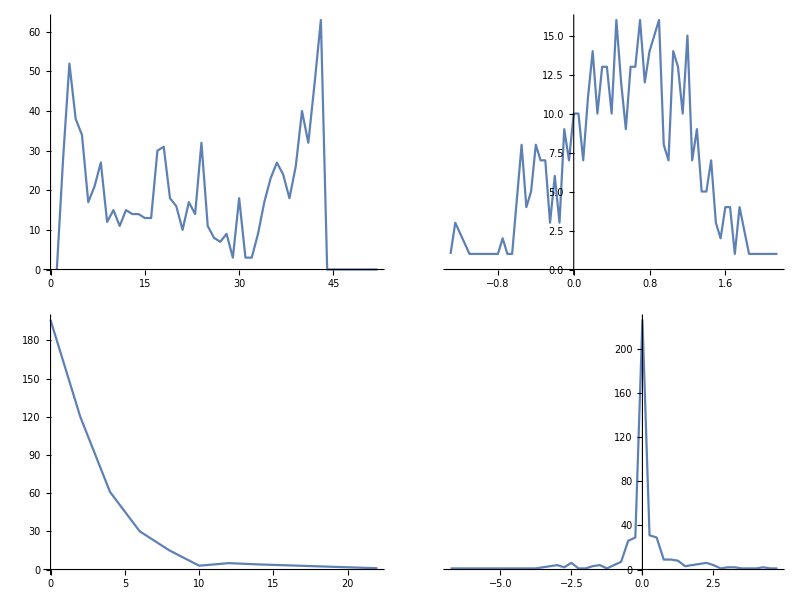

435

```mathematica
gapFreqs={{0,196},{2,120},{4,61},{6,30},{8,15},{10,3},{12,5},{14,4},{22,1}};
offsetDist={{-6.75,1},{-3.75,1},{-3.0,4},{-2.75,2},{-2.5,6},{-2.25,1},{-2.0,1},{-1.75,3},{-1.5,4},{-1.25,1},{-1.0,4},{-0.75,7},{-0.5,26},{-0.25,29},{0.0,226},{0.25,31},{0.5,29},{0.75,9},{1.0,9},{1.25,8},{1.5,3},{1.75,4},{2.0,5},{2.25,6},{2.5,4},{2.75,1},{3.0,2},{3.25,2},{3.5,1},{4.0,1},{4.25,2},{4.5,1},{4.75,1}};
scoreDist={{-1.3,1},{-1.25,3},{-1.1,1},{-0.8500000000000001,1},{-0.8,1},{-0.75,2},{-0.7000000000000001,1},{-0.65,1},{-0.55,8},{-0.5,4},{-0.45,5},{-0.4,8},{-0.35000000000000003,7},{-0.30000000000000004,7},{-0.25,3},{-0.2,6},{-0.15000000000000002,3},{-0.1,9},{-0.05,7},{0.0,10},{0.05,10},{0.1,7},{0.15000000000000002,11},{0.2,14},{0.25,10},{0.30000000000000004,13},{0.35000000000000003,13},{0.4,10},{0.45,16},{0.5,12},{0.55,9},{0.6000000000000001,13},{0.65,13},{0.7000000000000001,16},{0.75,12},{0.8,14},{0.8500000000000001,15},{0.9,16},{0.9500000000000001,8},{1.0,7},{1.05,14},{1.1,13},{1.1500000000000001,10},{1.2000000000000002,15},{1.25,7},{1.3,9},{1.35,5},{1.4000000000000001,5},{1.4500000000000002,7},{1.5,3},{1.55,2},{1.6,4},{1.6500000000000001,4},{1.7000000000000002,1},{1.75,4},{1.85,1},{1.9000000000000001,1},{2.0,1},{2.1,1},{2.15,1}};
gapOpenDist={0.0,28.0,52.0,38.0,34.0,17.0,21.0,27.0,12.0,15.0,11.0,15.0,14.0,14.0,13.0,13.0,30.0,31.0,18.0,16.0,10.0,17.0,14.0,32.0,11.0,8.0,7.0,9.0,3.0,18.0,3.0,3.0,9.0,17.0,23.0,27.0,24.0,18.0,26.0,40.0,32.0,47.0,63.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};



numAlignments=Total[Table[offsetDist[[i]][[2]],{i,1,Length[offsetDist]}]];

avgScore=Total[Table[scoreDist[[i]][[1]]*scoreDist[[i]][[2]],{i,1,Length[scoreDist]}]]/numAlignments;

avgGaps=Total[Table[gapFreqs[[i]][[1]]*gapFreqs[[i]][[2]],{i,1,Length[gapFreqs]}]]/numAlignments;

avgOffset=Total[Table[offsetDist[[i]][[1]]*offsetDist[[i]][[2]],{i,1,Length[offsetDist]}]]/numAlignments;

numAlignments
avgScore
avgOffset
N[avgGaps]
a=ListLinePlot[gapOpenDist];
b=ListLinePlot[scoreDist];
c=ListLinePlot[gapFreqs];
d=ListLinePlot[offsetDist,PlotRange->All];
GridBox[{{a,b},{c,d}}]//DisplayForm
Binomial[30,2]
```